# Wide-Range Temperature Probe

#### Basic Usage

Open the device:

```mathematica
sensor=DeviceOpen["Vernier"]
```

DeviceObject[…]

Get a single sensor measurement:

```mathematica
DeviceRead[sensor]
```

21.4347 mA

Take measurements every 0.25 seconds, for a total of 10 seconds:

```mathematica
data=DeviceReadTimeSeries[sensor,{10,0.25}]
```

TimeSeries[…]

Visualize the time series:

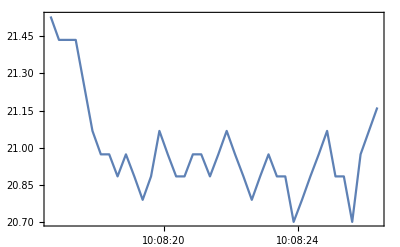

```mathematica
DateListPlot[data,PlotRange->All]
```

Close the device connection:

```mathematica
DeviceClose[sensor]
```

#### Advanced Usage

-Graphics-

Open the device:

```mathematica
sensor=DeviceOpen["Vernier"]
```

DeviceObject[…]

Schedule a task that takes one temperature reading every second:

```mathematica
RemoveScheduledTask/@ScheduledTasks[];
```

```mathematica
data={};

task=RunScheduledTask[
AppendTo[data,{Now,QuantityMagnitude@DeviceRead[sensor]}]
,1]
```

ScheduledTaskObject[…]

```mathematica
Dynamic[
DateListPlot[TimeSeries[data],
PlotRange->{0,All},
Filling->0]]
```

Remove the task and close the device:

```mathematica
RemoveScheduledTask[task];
DeviceClose[sensor];
```

### Science Experiments

#### Newton’s Law Of Cooling

```mathematica
FormulaData["NewtonsLawOfCooling"]
```

dQ/dt Power==A Area h HeatTransferCoefficient (-T Temperature+T_2 Temperature)